```mathematica
f1 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.375)]+0.5,0.25≤x<0.75},{0.5,0≤x<0.25},{0,0.75≤x≤1}}]+RandomReal[{0,0.1}],{x,0,1, 1/100}]
f2 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.5)]+0.5,0.375≤x<0.875},{0.5,0≤x<0.25},{0, 0.25≤ x < 0.375},{0,0.875≤x≤1}}] +RandomReal[{0,0.1}], {x, 0,1,1/100}]
f3 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.375)]+0.5,0.25≤x<0.75},{0.5,0≤x<0.25},{0,0.75≤x≤1}}] +RandomReal[{0,0.1}], {x, 0,1,1/1000}];
f4 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.5)]+0.5,0.375≤x<0.875},{0.5,0≤x<0.25},{0, 0.25≤ x < 0.375},{0,0.875≤x≤1}}] +RandomReal[{0,0.1}], {x, 0,1,1/1000}];
```

{0.539914,0.552764,0.562742,0.540124,0.562686,0.599209,0.589281,0.582965,0.597586,0.564947,0.525502,0.595601,0.593928,0.540563,0.534757,0.570062,0.528807,0.506083,0.535284,0.569803,0.500502,0.537855,0.511016,0.527816,0.581399,0.019095,0.0670862,0.110152,0.0651241,0.0656714,0.174187,0.190334,0.200963,0.281689,0.379972,0.362089,0.446298,0.520375,0.624333,0.642735,0.678174,0.747816,0.792901,0.893434,0.888568,0.963911,1.01808,1.00389,1.07266,1.03707,1.07892,1.08114,1.0282,1.03943,0.959564,1.00009,0.877541,0.880921,0.826627,0.71593,0.749605,0.609412,0.562913,0.542138,0.474528,0.437459,0.338389,0.309367,0.213188,0.214256,0.0956385,0.159737,0.0527796,0.0887186,0.0870789,0.0331369,0.0716025,0.0182714,0.0746073,0.0172594,0.0990511,0.0580099,0.0542157,0.0572566,0.0709605,0.00799705,0.0798304,0.0679181,0.0238828,0.08435,0.0560971,0.0441514,0.0469406,0.00582929,0.0437582,0.0403747,0.0792535,0.00931532,0.0383056,0.0870851,0.0189275}

{0.546177,0.506596,0.567285,0.513359,0.53957,0.597808,0.532929,0.50904,0.53038,0.514979,0.513428,0.564945,0.571125,0.59309,0.505039,0.520448,0.52791,0.585096,0.53461,0.537982,0.583547,0.507535,0.517455,0.519417,0.528359,0.086214,0.00465222,0.0214059,0.00351498,0.0683924,0.0770567,0.00517141,0.0934663,0.0895697,0.0797767,0.0943776,0.0807765,0.00804278,0.0739254,0.0396458,0.0997687,0.12827,0.102228,0.138261,0.226838,0.274916,0.305422,0.333099,0.463103,0.529714,0.502888,0.58196,0.681336,0.697068,0.76072,0.864029,0.852833,0.917464,0.983179,1.00559,1.0637,1.04831,1.00624,1.01493,1.01249,1.06544,1.04676,0.995626,0.930719,0.928058,0.839806,0.810609,0.742105,0.694004,0.630999,0.575715,0.449023,0.468647,0.332549,0.282066,0.243491,0.253532,0.188266,0.117972,0.14707,0.0925625,0.0945225,0.0930499,0.0849794,0.0865436,0.0398844,0.0984334,0.0994573,0.0785347,0.0632794,0.0692675,0.0396598,0.0295188,0.0704987,0.0349201,0.0281059}

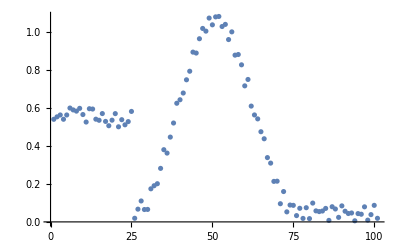

```mathematica
ListPlot[f1]
```

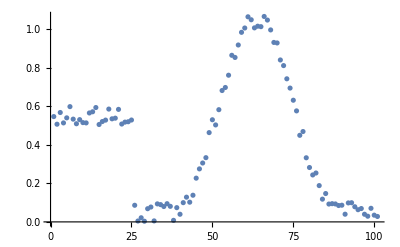

```mathematica
ListPlot[f2]
```

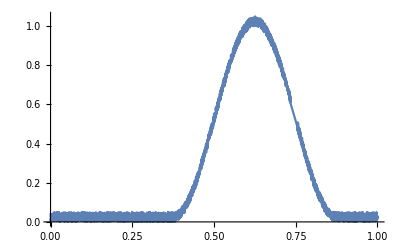

```mathematica
Plot[Piecewise[{{0.5*Sin[4*Pi*(x-0.5)]+0.5,0.375≤x<0.875},{0,0≤x<0.375},{0,0.875≤x≤1}}]+RandomReal[{0,0.05}],{x,0,1}]
```

```mathematica
Export[NotebookDirectory[]<>"plot1.svg",ListPlot[f1]]
Export[NotebookDirectory[]<>"plot2.svg", ListPlot[f2]]
Export[NotebookDirectory[]<>"plot3.svg",ListPlot[f3]]
Export[NotebookDirectory[]<>"plot4.svg", ListPlot[f4]]
```

/home/staff/scherping/Build/plot1.svg

/home/staff/scherping/Build/plot2.svg

/home/staff/scherping/Build/plot3.svg

/home/staff/scherping/Build/plot4.svg

```mathematica
Export[NotebookDirectory[]<>"plot1.csv", f1]
Export[NotebookDirectory[]<>"plot2.csv", f2]
Export[NotebookDirectory[]<>"plot3.csv", f3]
Export[NotebookDirectory[]<>"plot4.csv", f4]
```

/home/staff/scherping/Build/plot1.csv

/home/staff/scherping/Build/plot2.csv

/home/staff/scherping/Build/plot3.csv

/home/staff/scherping/Build/plot4.csv